```mathematica
ClearAll;
Rx = 1/(√2)*({{√2, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, √2, 0, 0}, {0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, -1, 0}});
```

```mathematica
z6 = ConstantArray[0,{6,6}];
z3 = ConstantArray[0,{3,3}];
Δ = 1/4;
(*w=1/40;
k=w*Δ;*)
dim = 18
```

18

```mathematica
Rx18 = ConstantArray[0,{dim,dim}];
For[i=1,i<dim,i=i+6,Rx18[[i;;i+5,i;;i+5]]=Rx];
Rx18 // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0)

```mathematica
adagQx= Transpose[Rx18].DiagonalMatrix[{0,1,1,0,-1,-1,0,1,1,0,-1,-1,0,1,1,0,-1,-1}].Rx18;
adagQx // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)

```mathematica
StencilP={1/Δ *{-1,1,0},1/Δ *{-1,1,0},1/Δ *{-1,1,0}};
StencilM ={1/Δ *{0,-1,1 },1/Δ *{0,-1,1 },1/Δ *{0,-1,1 }};
SvUpper= ArrayReshape[{Transpose[{IdentityMatrix[3],z3}],Transpose[{z3, z3}]},{6,6}];
SvLower = ArrayReshape[{Transpose[{z3,z3}],Transpose[{z3, IdentityMatrix[3]}]},{6,6}];
Sv =ConstantArray[0,{dim,dim}]; 
For[i=1,i<4,i=i+1,
For[j=0, j<3,j=j+1,Sv[[j*6+1;;(j+1)*6 ,j*6+1;;(j+1)*6 ]]+=(SvUpper*StencilM[[j+1,i]] + SvLower*StencilP[[j+1,i]])*Exp[-ⅈ*k*Δ*(i-2 + j - 1)]]]
Svk[k_] = Sv;
MatrixForm[Svk[k]]
```

(4-4 ⅇ^((ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4-4 ⅇ^((ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4-4 ⅇ^((ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 ⅇ^((ⅈ k)/4)-4 ⅇ^((ⅈ k)/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 ⅇ^((ⅈ k)/4)-4 ⅇ^((ⅈ k)/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 ⅇ^((ⅈ k)/4)-4 ⅇ^((ⅈ k)/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4+4 ⅇ^(-(ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4+4 ⅇ^(-(ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4+4 ⅇ^(-(ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4-4 ⅇ^((ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4-4 ⅇ^((ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4-4 ⅇ^((ⅈ k)/4) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4+4 ⅇ^(-(ⅈ k)/4) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4+4 ⅇ^(-(ⅈ k)/4) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4+4 ⅇ^(-(ⅈ k)/4))

```mathematica
step[k_] = adagQx.Transpose[Rx18].Svk[k].Rx18 ;
step[k] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (4-4 ⅇ^((ⅈ k)/4))+1/2 (-4 ⅇ^((ⅈ k)/4)+4 ⅇ^((ⅈ k)/2)) | 0 | 0 | 0 | 1/2 (-4+4 ⅇ^((ⅈ k)/4))+1/2 (-4 ⅇ^((ⅈ k)/4)+4 ⅇ^((ⅈ k)/2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (4-4 ⅇ^((ⅈ k)/4))+1/2 (-4 ⅇ^((ⅈ k)/4)+4 ⅇ^((ⅈ k)/2)) | 0 | 1/2 (4-4 ⅇ^((ⅈ k)/4))+1/2 (4 ⅇ^((ⅈ k)/4)-4 ⅇ^((ⅈ k)/2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (4-4 ⅇ^((ⅈ k)/4))+1/2 (4 ⅇ^((ⅈ k)/4)-4 ⅇ^((ⅈ k)/2)) | 0 | 1/2 (4-4 ⅇ^((ⅈ k)/4))+1/2 (-4 ⅇ^((ⅈ k)/4)+4 ⅇ^((ⅈ k)/2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-4+4 ⅇ^((ⅈ k)/4))+1/2 (-4 ⅇ^((ⅈ k)/4)+4 ⅇ^((ⅈ k)/2)) | 0 | 0 | 0 | 1/2 (4-4 ⅇ^((ⅈ k)/4))+1/2 (-4 ⅇ^((ⅈ k)/4)+4 ⅇ^((ⅈ k)/2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (-4+4 ⅇ^((ⅈ k)/4)) | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (-4+4 ⅇ^((ⅈ k)/4)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (-4+4 ⅇ^((ⅈ k)/4)) | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (4-4 ⅇ^((ⅈ k)/4)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (4-4 ⅇ^((ⅈ k)/4)) | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (-4+4 ⅇ^((ⅈ k)/4)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (-4+4 ⅇ^((ⅈ k)/4)) | 0 | 0 | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (-4+4 ⅇ^((ⅈ k)/4)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (-4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2)) | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (4 ⅇ^(-(ⅈ k)/4)-4 ⅇ^(-(ⅈ k)/2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (-4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2)) | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (-4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-4+4 ⅇ^(-(ⅈ k)/4))+1/2 (-4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2)) | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (-4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (4 ⅇ^(-(ⅈ k)/4)-4 ⅇ^(-(ⅈ k)/2)) | 0 | 0 | 0 | 1/2 (4-4 ⅇ^(-(ⅈ k)/4))+1/2 (-4 ⅇ^(-(ⅈ k)/4)+4 ⅇ^(-(ⅈ k)/2)))

{{w[k]→-4 ⅈ (-1+ⅇ^((ⅈ k)/4))},{w[k]→-4 ⅈ (-1+ⅇ^((ⅈ k)/4))},{w[k]→4 ⅈ (-1+ⅇ^((ⅈ k)/4))},{w[k]→4 ⅈ (-1+ⅇ^((ⅈ k)/4))},{w[k]→-4 ⅈ+4 ⅈ ⅇ^(-(ⅈ k)/4)},{w[k]→-4 ⅈ+4 ⅈ ⅇ^(-(ⅈ k)/4)},{w[k]→4 ⅈ-4 ⅈ ⅇ^(-(ⅈ k)/4)},{w[k]→4 ⅈ-4 ⅈ ⅇ^(-(ⅈ k)/4)},{w[k]→4 ⅈ ⅇ^((ⅈ k)/4) (-1+ⅇ^((ⅈ k)/4))},{w[k]→4 ⅈ ⅇ^((ⅈ k)/4) (-1+ⅇ^((ⅈ k)/4))},{w[k]→-4 ⅈ ⅇ^(-(ⅈ k)/2) (-1+ⅇ^((ⅈ k)/4))},{w[k]→-4 ⅈ ⅇ^(-(ⅈ k)/2) (-1+ⅇ^((ⅈ k)/4))}}

-4 ⅈ (-1+ⅇ^((ⅈ k)/4))

-4 ⅈ+4 ⅈ ⅇ^(-(ⅈ k)/4)

4 ⅈ ⅇ^((ⅈ k)/4) (-1+ⅇ^((ⅈ k)/4))

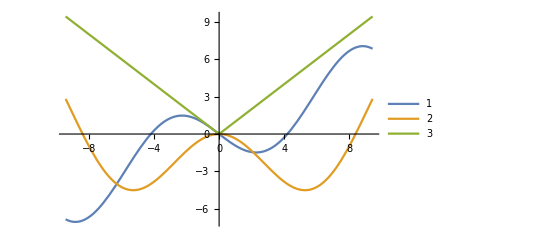

```mathematica
Element[k,Reals];
wsol[k_] = Simplify[Solve[Det[ⅈ*w[k]*IdentityMatrix[dim] + step[k]]==0 && w[k]!=0 ,w[k], Complexes]]
w1[k_]= w[k]/.wsol[k][[1]]
w2[k_]= w[k]/.wsol[k][[5]]
w3[k_]= w[k]/.wsol[k][[10]]
Plot[{Re[w3[k]], Im[w3[k]],Abs[k]},{k,-3.14*3,3.14*3},PlotLegends->{"1","2","3"}]
```